FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

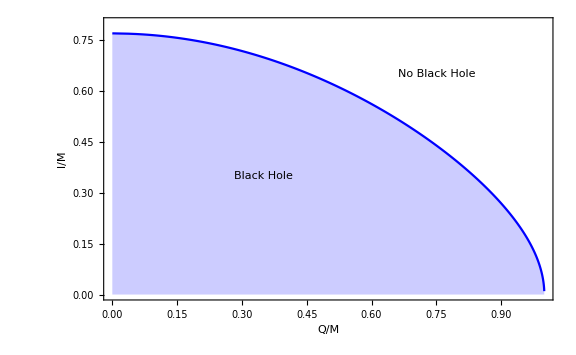

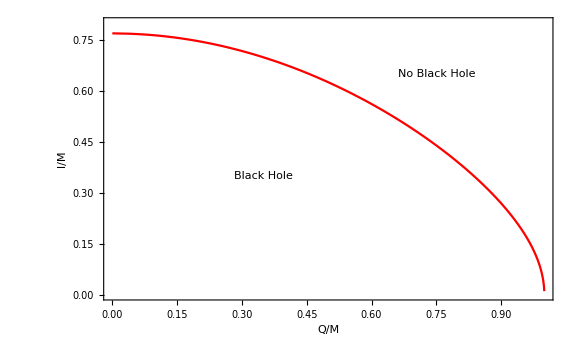

```mathematica
f[r_,Q_,l_]:= 1 - ((2*r-Q^2)*r^2)/(r^4+(2*r+Q^2)l^2);
ll=Table[l,{l,0.01,0.77,0.001}];
QQ=Table[Q/.FindRoot[{(f[r,Q,l]/.{l->ll[[i]]})==0,D[(f[r,Q,l]/.{l->ll[[i]]}),r]==0},{{r,1},{Q,1}}],{i,1,Length[ll]}];
QQll=Table[{QQ[[i]],ll[[i]]},{i,1,Length[ll]}];
ListLinePlot[QQll,Frame->True,FrameLabel->{"Q/M","l/M"},Filling->Axis,LabelStyle->Directive[FontFamily->"Times",FontSize->14,FontColor->Black],PlotStyle->Blue,PlotRange->{{0.,1},{0,0.8}},BaseStyle->{14,FontFamily->"TimesNewRoman"},
Epilog->{Text[Rotate[Framed["Black Hole",FrameStyle->None,Background->None],0Degree],{0.35,0.35}],Text[Rotate[Framed["No Black Hole",FrameStyle->None,Background->None],0Degree],{0.75,0.65}]},ImageSize->Large]
ListLinePlot[QQll,Frame->True,FrameLabel->{"Q/M","l/M"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,FontColor->Black],PlotStyle->Red,PlotRange->{{0.,1},{0,0.8}},BaseStyle->{14,FontFamily->"TimesNewRoman"},
Epilog->{Text[Rotate[Framed["Black Hole",FrameStyle->None,Background->None],0Degree],{0.35,0.35}],Text[Rotate[Framed["No Black Hole",FrameStyle->None,Background->None],0Degree],{0.75,0.65}]},ImageSize->Large]
```

```mathematica
-Graphics-;
```

```mathematica
-Graphics-;
```